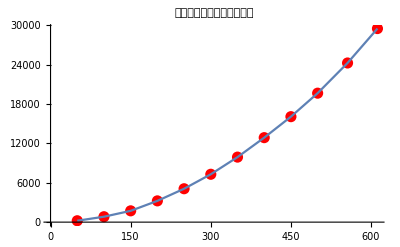

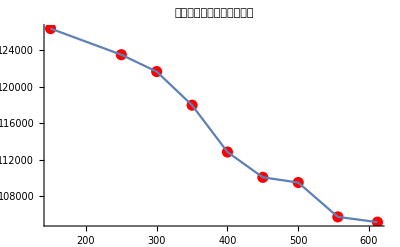

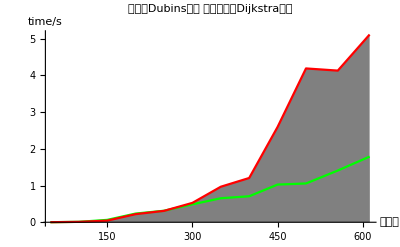

```mathematica
(*附件1*)
statistic={{50,212,0.0009953975677490234},{100,826,0.010971546173095703},{150,1722,0.06479310989379883},{200,3240,0.23636841773986816},{250,5088,0.3132054805755615},{300,7293,0.48769426345825195},{350,9906,0.653374195098877},{400,12872,0.7076218128204346},{450,16068,1.02581787109375},{500,19648,1.0557458400726318},{556,24248,1.4083187580108643},{612,29491,1.7877309322357178}};
bianshu=DropCol[statistic,{3}];
putongtime=DropCol[statistic,{2}];
dubinstime={{50,0.0009982585906982422},{100,0.010971546173095703},{150,0.043882131576538086},{200,0.2203676700592041},{250,0.30974745750427246},{300,0.527110099792480},{350,0.9664897918701172},{400,1.2048399448394775},{450,2.594172477722168},{500,4.187292575836182},{556,4.1280434131622314},{612,5.109937906265259}};
hangchang={{150,126347.37207},{250,123486.65380},{300,121638.55810},{350,117961.39062},{400,112836.40234},{450,110065.78418},{500,109498.85341},{556,105737.01121},{612,105163.22399}};

Show[ListPlot[bianshu,PlotStyle->{PointSize[0.02],Red}],ListLinePlot@bianshu,PlotLabel->"网络边数随节点数增加趋势",AxesLabel->{"节点数"}]
Show[ListPlot[hangchang,PlotStyle->{PointSize[0.02],Red}],ListLinePlot@hangchang,PlotLabel->"航迹航程随节点数增加减小",AxesLabel->{"节点数"}]
ListLinePlot[{putongtime,dubinstime},AxesLabel->{"节点数","time/s"},PlotStyle->{Green,Red},PlotRange->All,Filling->Axis,FillingStyle->Gray,PlotLabel->"红色：Dubins优化 绿色：改进Dijkstra算法"]
```

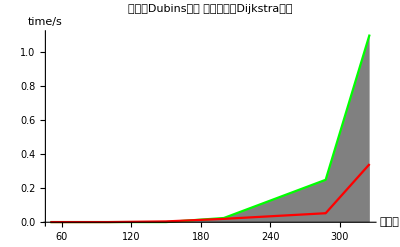

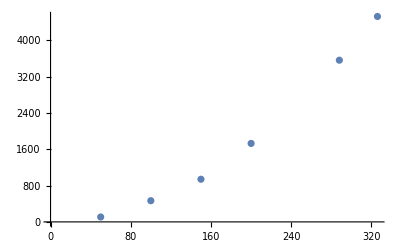

```mathematica
(*附件2*)
statistic={{50,108,0.0009996891021728516},{100,467,0.0009970664978027344},{150,940,0.000995635986328125},{200,1729,0.024932384490966797},{288,3563,0.24884986877441406},{326,4527,1.1000182628631592}};
bianshu=DropCol[statistic,{3}];
dubinstime={{50,0.0009992122650146484},{100,0.0010342597961425781},{150,0.004952430725097656},{200,0.019904613494873047},{288,0.05289912223815918},{326,0.34108638763427734}};
putongtime=DropCol[statistic,{2}];
ListLinePlot[{putongtime,dubinstime},AxesLabel->{"节点数","time/s"},PlotStyle->{Green,Red},PlotRange->All,Filling->Axis,FillingStyle->Gray,PlotLabel->"红色：Dubins优化 绿色：改进Dijkstra算法"]
ListPlot@bianshu
```